## Lesson

Flatten sublists:

```mathematica
Flatten[{{1,2},{3,4}}]
```

{1,2,3,4}

Create graph with list of rules:

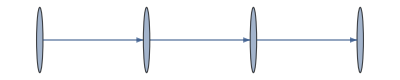

```mathematica
Graph[{1->2,2->3,3->4}]
```

Create undirected graph:

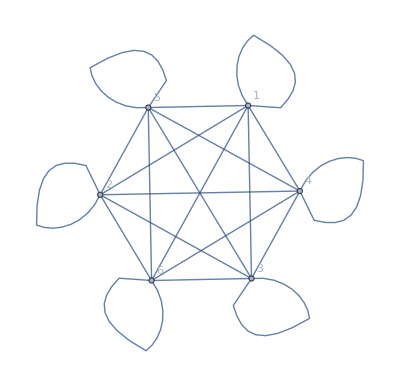

```mathematica
UndirectedGraph[Flatten[Table[i->j,{i,6},{j,6}]],VertexLabels->Automatic]
```

Display a graph arranged into “communities” :

```mathematica
CommunityGraphPlot[Graph[Table[RandomInteger[10]->RandomInteger[10],20],VertexLabels->All]]
```

-Graphics-

Find shortest path between two nodes in a graph:

```mathematica
FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],4,2]
```

{4,1,2}

## Questions

Q1. Make a graph consisting of a loop of 3 nodes.



```mathematica
Graph[Table[i->Mod[i,3]+1,{i,3}]]
```

Q2. Make a graph with 4 nodes in which every node is connected.

```mathematica
Graph[Flatten[Table[i->j,{i,4},{j,4}]]]
```

-Graphics-

Q3. Make a table of undirected graphs with between 2 and 10 nodes in which every node is connected.

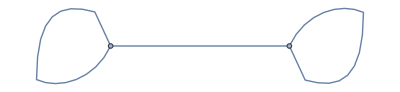
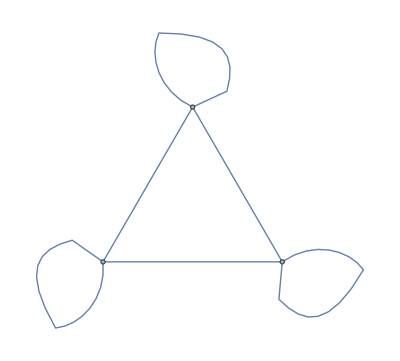
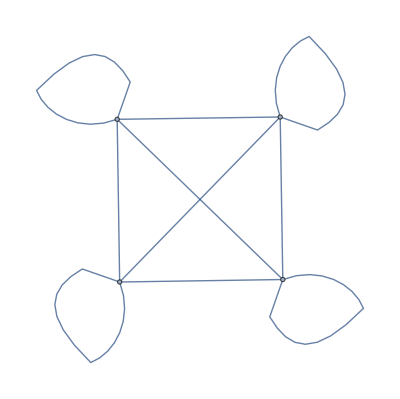
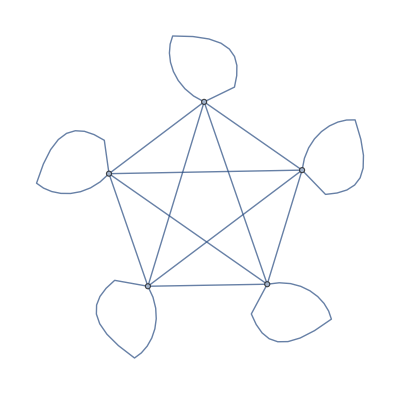
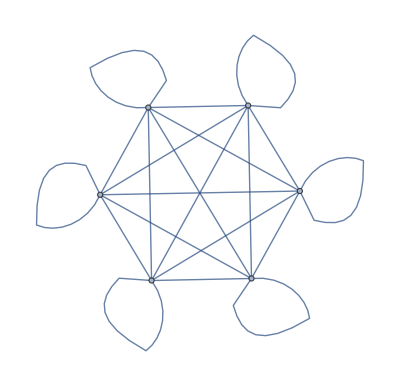
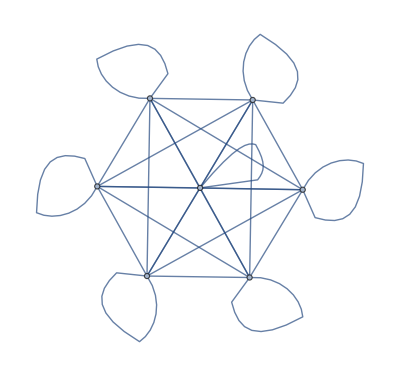
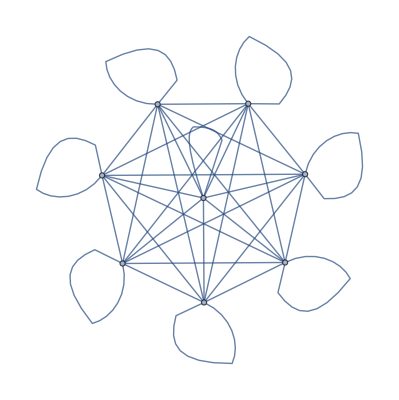
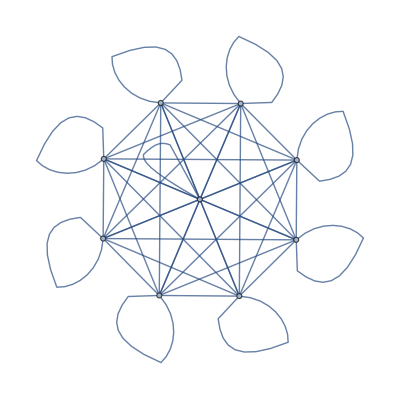

```mathematica
UndirectedGraph[Flatten[Table[i->j,{i,#},{j,#}]]]&/@Range[2,10]
```

Q4. Use Table and Flatten to get {1, 2, 1, 2, 1, 2}.

```mathematica
Flatten[Table[{1,2},3]]
```

{1,2,1,2,1,2}

Q5. Make a line plot of the result of concatenating all digits of all integers from 1 to 100 (i.e. ..., 8, 9, 1, 0, 1, 1, 1, 2, ...).

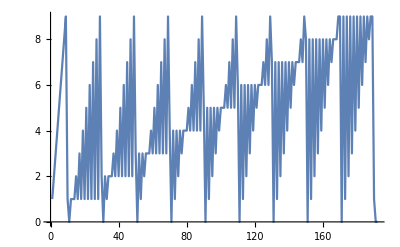

```mathematica
ListLinePlot[Flatten[IntegerDigits[Range[100]]]]
```

Q6. Make a graph with 50 nodes, in which node i connects to node i+1.

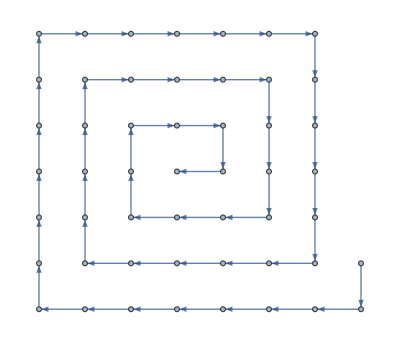

```mathematica
Graph[Table[i->i+1,{i,50}]]
```

Q7. Make a graph with 4 nodes, in which each connection connects i to Max[i, j].

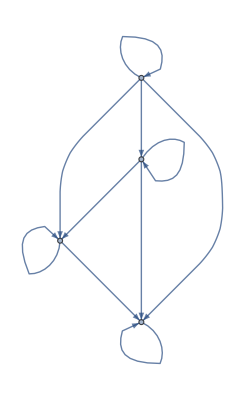

```mathematica
Graph[Flatten[Table[i->j,{i,4},{j,i,4}]]]
```

Q8. Make a graph in which each connection connects i to j-i, where i and j both range from 1 to 5.

```mathematica
Graph[Flatten[Table[i->j-i,{i,5},{j,5}]]]
```

-Graphics-

Q9. Generate a graph with 100 nodes, each with a connection going to one randomly chosen node.

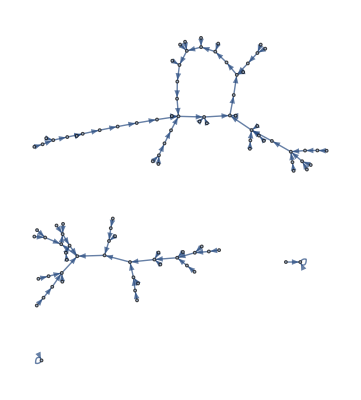

```mathematica
Graph[#->RandomInteger[{1,100}]&/@Range[100]]
```

Q10. Generate a graph with 100 nodes, each connecting to two randomly chosen nodes.

```mathematica
Graph[Flatten[{#->RandomInteger[{1,100}],#->RandomInteger[{1,100}]}&/@Range[100]]]
```

-Graphics-

Q11. For the graph {1→2, 2→3, 3→4, 4→1, 3→1, 2→2}, make a grid giving the shortest paths between every pair of nodes, with the start node as row and end node as column.

```mathematica
Grid[With[{graph={1->2,2->3,3->4,4->1,3->1,2->2}},Table[FindShortestPath[graph,i,j],{i,4},{j,4}]]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

## Extended Questions

+Q1. Make a graph with 4 nodes in which every node is connected, displaying the resulting graph with radial drawing.

```mathematica
Graph[Flatten[Table[i->j,{i,4},{j,4}]],GraphLayout->"RadialDrawing"]
```

-Graphics-

+Q2. Generate a graph in which a single node is connected to 10 others

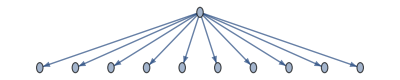

```mathematica
Graph[0->#&/@Range[10]]
```

+Q3. Use Flatten to generate a table of the numbers 1 to 50 in which even numbers are coloured red.

```mathematica
Flatten[Table[{i, Style[i+1,Red]},{i,1,50,2}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

+Q4. Use ImageData, Flatten and Total to find the number of white pixels in Binarize[Rasterize[“W”]].

```mathematica
Total[ImageData[Binarize[Rasterize["W"]]],2]
```

186

+Q5. Use Flatten, IntegerDigits and Total to find the sum of all digits of all whole numbers up to 1000.

```mathematica
Total[IntegerDigits[Range[1000]],2]
```

13501

+Q6. Generate a graph with 200 connections, each between nodes with numbers randomly chosen between 0 and 100.

```mathematica
Graph[Table[RandomInteger[100]->RandomInteger[100],200]]
```

-Graphics-

+Q7. Generate a plot that shows communities in a random graph with nodes numbered between 0 and 100, and 200 connections.

```mathematica
CommunityGraphPlot[Graph[Table[RandomInteger[100]->RandomInteger[100],200]]]
```

-Graphics-